## Code. First cell is symbolic checker for parameters.

L = 4

nParticles = 2

Extra bits for moves: 0

J Matrix:

(0 | J01 | J02
J01 | 0 | J12
J02 | J12 | 0)

Total configurations: 12

First few: {{1,2,0,0},{2,1,0,0},{1,0,2,0},{2,0,1,0},{1,0,0,2}}

Transition matrix row sums: {1,1,1,1,1,1,1,1,1,1,1,1}

Transition matrix:

(1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 1/4 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0
1/4 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0
1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1-(Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}])
0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1-(Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0
0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 1/4 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0
0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 1/4 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0
0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 1/4 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0
0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 1/4 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0
0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1-(Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0
1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1-(Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}])
0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 1/4
0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 1/4 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])))

Computing detailed balance violations...

Non-literal-zero violations: 16

Unique violations to simplify: 2 (reduced from 16)

Applying FullSimplify to unique violations...

Detailed balance: SATISFIED (all unique violations symbolically reduced to 0)

Decision tree for first state:

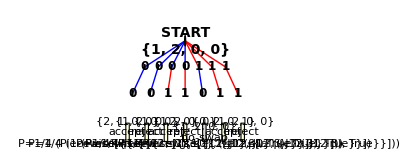

Decision tree for second state:

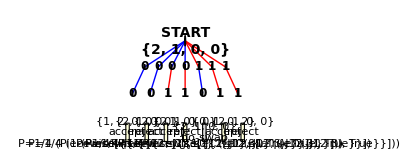

```mathematica
ClearAll["Global`*"]




(* =========================================*)
(*SETUP-DEFINE SYSTEM PARAMETERS*)
(* =========================================*)

L=4;              (*Lattice size-number of sites on the ring*)
nParticles=2;     (*Number of distinguishable particles to place on lattice*)
β=Symbol["β"];  (*Inverse temperature-kept symbolic*)

(*SELECT WHICH KAWASAKI FUNCTION TO USE*)
TESTFUNCTION=KawasakiMoveFromBitsDB;  (*Change to KawasakiMoveFromBits2 to switch*)


(*SPECIFY NUMBER OF EXTRA RANDOM BITS FOR THE MOVE*)
(*nExtraBits controls the complexity of the move:-0=standard Kawasaki (just nearest-neighbor swap)-1=enhanced moves (e.g.,reversal,translation)-2+ =even more complex moves requiring multiple decision bits*)
nExtraBits=0;

Print["L = ",L];
Print["nParticles = ",nParticles];
Print["Extra bits for moves: ",nExtraBits];

(* =========================================*)
(*SYMBOLIC J MATRIX-INTERACTION ENERGIES*)
(* =========================================*)

(*Generates a symmetric matrix of symbolic coupling constants J_ij J_ij represents the interaction energy between particle types i and j Matrix is (nParticles+1) x (nParticles+1) to include empty sites (type 0) Example for nParticles=2:creates J01,J02,J12 as symbolic variables*)
GenerateSymbolicJ[n_]:=Module[{J=Table[0,{n+1},{n+1}]},Do[If[i<j,(*Create symbolic variable for interaction*)J[[i+1,j+1]]=Symbol["J"<>ToString[i]<>ToString[j]];
(*Make matrix symmetric*)J[[j+1,i+1]]=J[[i+1,j+1]]],{i,0,n},{j,0,n}];
J]

JMatrix=GenerateSymbolicJ[nParticles];

Print["J Matrix:"];
Print[JMatrix//MatrixForm];

(* =========================================*)
(*ENERGY FUNCTION*)
(* =========================================*)

(*Calculates the energy of a lattice configuration Energy=-Σ J(particle_i,particle_j) for all nearest-neighbor pairs Uses periodic boundary conditions (ring topology) Only counts interactions between occupied sites (non-zero particles)*)
SymbolicEnergy[lattice_]:=Module[{E=0,i,j},Do[(*Get next neighbor with periodic boundaries*)j=If[i==Length[lattice],1,i+1];
(*Only add interaction if both sites are occupied*)If[lattice[[i]]!=0&&lattice[[j]]!=0,E-=JMatrix[[lattice[[i]]+1,lattice[[j]]+1]]],{i,Length[lattice]}];
E]

(* =========================================*)
(*CONFIGURATION GENERATION*)
(* =========================================*)

(*Generates all possible configurations of n distinguishable particles on L sites For L=4,n=2:produces 12 configurations (6 positions×2 permutations) Example:{1,2,0,0},{2,1,0,0},{1,0,2,0},etc.*)
GenerateAllConfigs[L_,n_]:=Flatten[Table[Module[{lat=ConstantArray[0,L]},(*Place particles at selected positions with given permutation*)Do[lat[[pos[[i]]]]=perm[[i]],{i,n}];
lat],{pos,Subsets[Range[L],{n}]},(*All ways to choose n positions*){perm,Permutations[Range[n]]}      (*All orderings of n particles*)],1]

states=GenerateAllConfigs[L,nParticles];
Print["Total configurations: ",Length[states]];
Print["First few: ",Take[states,Min[5,Length[states]]]];

(* =========================================*)
(*BINARY TREE RANDOMNESS INFRASTRUCTURE*)
(* =========================================*)

(*Global variables for tracking position in bit sequence $BinaryChoices:the current sequence of bits being processed $BinaryIndex:current read position (1-indexed)*)
$BinaryChoices={};
$BinaryIndex=1;

(*Reads one bit from the current bit sequence and advances the position This simulates reading a random bit,but deterministically from a fixed sequence*)
BinaryBit[]:=Module[{b},b=$BinaryChoices[[$BinaryIndex]];
$BinaryIndex++;
b]

(*Reads nBits from the sequence and interprets as a binary integer Example:{0,1,1} with nBits=3->0×4+1×2+1×1=3*)
DecodeInteger[nBits_]:=FromDigits[Table[BinaryBit[],{nBits}],2]

(* =========================================*)
(*KAWASAKI MOVE-MAIN DYNAMICS FUNCTION*)
(* =========================================*)

(* =========================================*)(*TWO-SITE KAWASAKI MOVE*)(* =========================================*)(*Selects TWO random lattice sites (instead of adjacent neighbors) and attempts to swap the particles at those positions Bit consumption:-First nBits:select site i-Second nBits:select site j-Total:2×nBits bits consumed This creates longer-range moves compared to nearest-neighbor Kawasaki Special cases:-If i=j:no-swap (can't swap site with itself)-If lattice[[i]]=lattice[[j]]:no-swap (same particle type) Returns:Same format as standard Kawasaki {{"accept",newState,probability},{"reject",oldState,probability}} or {"no-swap",state,probability}*)(*CORRECTED VERSION for use with nExtraBits*)



KawasakiMoveFromBits[lattice_]:=Module[{Lsize,nBits,rawI,rawJ,i,j,new,ΔE,p,siteProb},Lsize=Length[lattice];
nBits=Ceiling[Log2[Lsize]];
(*DON'T consume extra bits here-they're already accounted for! The "extra" bits ARE the second site selection bits*)(*REMOVED:If[nExtraBits>0,DecodeInteger[nExtraBits]];*)(*For L=4 with nExtraBits=2:-nBits=2 (first site)-nExtraBits=2 (second site)-Total=4 bits,siteProb=1/16*)siteProb=1/(2^(nBits+nExtraBits));
(*FIRST SITE:Read nBits*)rawI=DecodeInteger[nBits];
i=1+Mod[rawI,Lsize];
(*SECOND SITE:Read nExtraBits (which equals nBits for L=4)*)rawJ=DecodeInteger[nExtraBits];
j=1+Mod[rawJ,Lsize];
(*NO-SWAP CHECKS*)If[i==j,Return[{"no-swap",lattice,siteProb}]];
If[lattice[[i]]==lattice[[j]],Return[{"no-swap",lattice,siteProb}]];
(*PERFORM SWAP*)new=lattice;
new[[{i,j}]]=lattice[[{j,i}]];
(*ENERGY CHANGE*)ΔE=SymbolicEnergy[new]-SymbolicEnergy[lattice];
(*METROPOLIS ACCEPTANCE*)p=Piecewise[{{1,ΔE<=0},{Exp[-β ΔE],ΔE>0}}];
{{"accept",new,siteProb*p},{"reject",lattice,siteProb*(1-p)}}]

(*CURRENT VERSION-Standard Kawasaki Dynamics with Metropolis Acceptance*)
(*This function implements a single Monte Carlo move:1. Uses random bits to select a lattice site 2. Attempts to swap particles with the next neighbor 3. Accepts/rejects based on Metropolis criterion Returns:List of outcomes with their probabilities-If sites have same particle type:{{"no-swap",lattice,probability}}-Otherwise:{{"accept",newState,acceptProb},{"reject",oldState,rejectProb}}*)



KawasakiMoveFromBitsDB[lattice_]:=Module[{Lsize,nBits,raw,i,j,new,ΔE,p,siteProb},Lsize=Length[lattice];
(*Calculate bits needed:nBits for site selection+nExtraBits for enhancements*)nBits=Ceiling[Log2[Lsize]];

translated=RotateRight[lattice,0];
(*e.g.,L=4 needs 2 bits,L=8 needs 3 bits*)(*CONSUME EXTRA BITS (if any)-for enhanced moves like reversal/translation Currently nExtraBits=0,so this does nothing With nExtraBits=1,would read one bit here for a binary decision*)If[nExtraBits>0,DecodeInteger[nExtraBits]];
(*Probability weight for this branch of the decision tree With nBits=2,nExtraBits=0:siteProb=1/4 (one of 4 possible bit patterns)*)siteProb=1/(2^(nBits+nExtraBits));
(*SITE SELECTION:Read nBits to choose which site to attempt swap at*)raw=DecodeInteger[nBits];(*Consumes nBits from $BinaryChoices*)(*Map bit pattern to lattice site with modulo (handles 2^nBits>Lsize) Example:raw=3,Lsize=4->i=1+Mod[3,4]=4*)i=1+Mod[raw,Lsize];
(*Next site (periodic boundaries:site 4 connects back to site 1)*)j=If[i==Lsize,1,i+1];
(*NO-SWAP CHECK:If both sites have same particle type,nothing can happen This includes:both empty (0,0),or same particle (1,1),(2,2),etc.*)If[translated[[i]]==translated[[j]],Return[{"no-swap",lattice,siteProb}]];
(*PERFORM SWAP:Exchange particles at positions i and j*)new=translated;
new[[{i,j}]]=translated[[{j,i}]];
(*ENERGY CHANGE:Calculate ΔE=E_new-E_old*)ΔE=SymbolicEnergy[new]-SymbolicEnergy[translated];
(*METROPOLIS ACCEPTANCE PROBABILITY:-If ΔE≤0 (energy decreases or stays same):always accept (p=1)-If ΔE>0 (energy increases):accept with probability exp(-β×ΔE)*)p=Piecewise[{{1,ΔE<=0},{Exp[-β ΔE],ΔE>0}}];
(*RETURN TWO POSSIBLE OUTCOMES:1. "accept":move to new state with probability siteProb×p 2. "reject":stay in old state with probability siteProb×(1-p) These probabilities sum to siteProb (the weight of this branch)*){{"accept",new,siteProb*p},{"reject",translated,siteProb*(1-p)}}]


KawasakiMoveFromBitsnoDB[lattice_]:=Module[{Lsize,nBits,raw,i,j,new,ΔE,p,siteProb},Lsize=Length[lattice];
(*Calculate bits needed:nBits for site selection+nExtraBits for enhancements*)nBits=Ceiling[Log2[Lsize]];

translated=RotateRight[lattice,1];
(*e.g.,L=4 needs 2 bits,L=8 needs 3 bits*)(*CONSUME EXTRA BITS (if any)-for enhanced moves like reversal/translation Currently nExtraBits=0,so this does nothing With nExtraBits=1,would read one bit here for a binary decision*)If[nExtraBits>0,DecodeInteger[nExtraBits]];
(*Probability weight for this branch of the decision tree With nBits=2,nExtraBits=0:siteProb=1/4 (one of 4 possible bit patterns)*)siteProb=1/(2^(nBits+nExtraBits));
(*SITE SELECTION:Read nBits to choose which site to attempt swap at*)raw=DecodeInteger[nBits];(*Consumes nBits from $BinaryChoices*)(*Map bit pattern to lattice site with modulo (handles 2^nBits>Lsize) Example:raw=3,Lsize=4->i=1+Mod[3,4]=4*)i=1+Mod[raw,Lsize];
(*Next site (periodic boundaries:site 4 connects back to site 1)*)j=If[i==Lsize,1,i+1];
(*NO-SWAP CHECK:If both sites have same particle type,nothing can happen This includes:both empty (0,0),or same particle (1,1),(2,2),etc.*)If[translated[[i]]==translated[[j]],Return[{"no-swap",lattice,siteProb}]];
(*PERFORM SWAP:Exchange particles at positions i and j*)new=translated;
new[[{i,j}]]=translated[[{j,i}]];
(*ENERGY CHANGE:Calculate ΔE=E_new-E_old*)ΔE=SymbolicEnergy[new]-SymbolicEnergy[translated];
(*METROPOLIS ACCEPTANCE PROBABILITY:-If ΔE≤0 (energy decreases or stays same):always accept (p=1)-If ΔE>0 (energy increases):accept with probability exp(-β×ΔE)*)p=Piecewise[{{1,ΔE<=0},{Exp[-β ΔE],ΔE>0}}];
(*RETURN TWO POSSIBLE OUTCOMES:1. "accept":move to new state with probability siteProb×p 2. "reject":stay in old state with probability siteProb×(1-p) These probabilities sum to siteProb (the weight of this branch)*){{"accept",new,siteProb*p},{"reject",translated,siteProb*(1-p)}}]

(* =========================================*)
(*DECISION TREE ENUMERATION*)
(* =========================================*)

(*Enumerates ALL possible outcomes from a given lattice state For L=4,nExtraBits=0:explores 2^2=4 possible bit sequences Each bit sequence determines which site is selected for swap Returns:List of all possible outcomes with format:{{bitSequence,outcomeType,finalState,probability},...} Example entry:{{0,1},"accept",{1,0,2,0},1/4×exp(-β×ΔE)}*)
EnumerateTree[lattice_]:=Module[{nBitsForSite,nBitsTotal,allBits,results},(*Calculate total bits needed*)nBitsForSite=Ceiling[Log2[Length[lattice]]];
nBitsTotal=nBitsForSite+nExtraBits;
(*GENERATE ALL POSSIBLE BIT SEQUENCES For nBitsTotal=2:{{0,0},{0,1},{1,0},{1,1}}*)allBits=Tuples[{0,1},nBitsTotal];
(*FOR EACH BIT SEQUENCE,call KawasakiMoveFromBits and record outcome*)results=Flatten[Table[(*Set up the bit sequence for this iteration*)($BinaryChoices=bits;(*Set the bits to be read*)$BinaryIndex=1;(*Reset read position to start*)(*Call the move function-it will consume bits from $BinaryChoices*)With[{out=TESTFUNCTION[lattice]},(*UNPACK RESULT based on outcome type*)If[First[out]==="no-swap",(*No-swap case:single outcome*){{bits,"no-swap",out[[2]],out[[3]]}},(*Swap case:two outcomes (accept and reject)*){{bits,"accept",out[[1,2]],out[[1,3]]},{bits,"reject",out[[2,2]],out[[2,3]]}}]]),{bits,allBits}  (*Iterate over all bit sequences*)],1  (*Flatten by one level to get flat list*)];
results]

(* =========================================*)
(*TREE VISUALIZATION-GRAPHICAL DISPLAY*)
(* =========================================*)

(*Creates a scrollable visualization of the decision tree Shows all possible bit sequences as paths from root to leaves Color coding:Blue=0 bit,Red=1 bit Leaves show:final state,outcome type (accept/reject/no-swap),probability*)
VisualizeDecisionTree[initialState_]:=Module[{tree,nBitsForSite,nBitsTotal,yLevels,xSpacing,nodeRadius,rootX,rootY,pathGraphics,baseXPositions,imageWidth,plotRangeX,Lsize,rootGraphics},(*Generate the decision tree*)tree=EnumerateTree[initialState];
Lsize=Length[initialState];
nBitsForSite=Ceiling[Log2[Lsize]];
nBitsTotal=nBitsForSite+nExtraBits;
(*Layout parameters-create wide scrollable canvas*)imageWidth=Max[1800,Length[tree]*60];
plotRangeX=Max[50,Length[tree]*3];
yLevels=Range[nBitsTotal,0,-1]*2;(*Vertical positions for each bit level*)xSpacing=Max[20,Length[tree]*1.5];
nodeRadius=0.2;
rootX=0;
rootY=yLevels[[1]];
(*Horizontal positions for leaf nodes (spread evenly)*)baseXPositions=Table[(i-(Length[tree]+1)/2)*(xSpacing/1.5),{i,Length[tree]}];
(*GENERATE GRAPHICS FOR EACH PATH through the tree*)pathGraphics=Table[Module[{path,pathType,finalState,probability,currentX,currentY,lineGraphics,circleGraphics,labelGraphics,bit,level,nextX,nextY,edgeColor,leafY,leafX,leafColor,leafText,treeEntry},(*Unpack tree entry*)treeEntry=tree[[i]];
path=Part[treeEntry,1];(*Bit sequence*)pathType=Part[treeEntry,2];(*"accept","reject",or "no-swap"*)finalState=Part[treeEntry,3];(*Resulting lattice configuration*)probability=Part[treeEntry,4];(*Probability of this outcome*)(*Start at root*)currentX=rootX;
currentY=rootY;
lineGraphics={};
circleGraphics={};
labelGraphics={};
(*DRAW PATH:For each bit in the sequence*)Do[bit=path[[level]];
(*Calculate next node position (converging toward final x position)*)nextX=baseXPositions[[i]]+(currentX-baseXPositions[[i]])*0.3;
nextY=yLevels[[level+1]];
(*Color edges:Blue for 0,Red for 1*)edgeColor=Which[bit==0,Blue,bit==1,Red,True,Black];
(*Draw edge from current to next position*)AppendTo[lineGraphics,{edgeColor,Thickness[0.0025],Arrowheads[0],Arrow[{{currentX,currentY},{nextX,nextY}}]}];
(*Draw node circle*)AppendTo[circleGraphics,{White,EdgeForm[{Black,Thin}],Disk[{nextX,nextY},nodeRadius]}];
(*Label node with bit value*)AppendTo[labelGraphics,Text[Style[bit,Bold,12],{nextX,nextY}]];
(*Move to next position*)currentX=nextX;
currentY=nextY;,{level,Length[path]}];
(*DRAW LEAF NODE at bottom*)leafY=-3;
leafX=baseXPositions[[i]];
(*Format leaf label based on outcome type*){leafColor,leafText}=Which[pathType=="no-swap",{LightGray,Column[{Style[ToString[finalState],Gray,12],Style["no-swap",Gray,10]},Center,Spacings->0.1]},pathType=="accept",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["accept",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]},pathType=="reject",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["reject",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]}];
(*Draw leaf rectangle*)AppendTo[circleGraphics,{leafColor,EdgeForm[{Black,Thin}],Rectangle[{leafX-1.2,leafY-0.7},{leafX+1.2,leafY+0.7}]}];
(*Add leaf label*)AppendTo[labelGraphics,Text[leafText,{leafX,leafY}]];
(*Return graphics for this path*){lineGraphics,circleGraphics,labelGraphics}],{i,Length[tree]}];
(*DRAW ROOT NODE*)rootGraphics={{LightBlue,EdgeForm[{Black,Thick}],Disk[{rootX,rootY},nodeRadius*2]},Text[Style["START\n"<>ToString[initialState],Bold,14],{rootX,rootY}]};
(*COMBINE AND WRAP in scrollable pane*)Pane[Graphics[{pathGraphics,rootGraphics},PlotRange->{{-plotRangeX,plotRangeX},{-4,yLevels[[1]]+2}},AspectRatio->0.4,Background->White],{1800,600},(*Pane size*)Scrollbars->True]]

(* =========================================*)
(*TRANSITION PROBABILITY CALCULATION*)
(* =========================================*)

(*Converts decision tree into state-to-state transition probabilities Multiple bit sequences can lead to same state transition This function merges them by summing their probabilities Example:{1,2,0,0}->{1,2,0,0} might occur via:-bits {1,0} causing "no-swap" (prob 1/4)-bits {0,0} causing swap with rejection (prob 1/4×(1-p)) Total probability=1/4+1/4×(1-p)*)
EnumerateTransitions[lattice_]:=Module[{tree},(*Get all outcomes from this state*)tree=EnumerateTree[lattice];
(*Group by (fromState,toState) pair and sum probabilities Merge with Total:combines duplicate keys by adding values*)Merge[Table[{lattice,tree[[i,3]]}->tree[[i,4]],{i,Length[tree]}],Total]]

(* =========================================*)
(*TRANSITION MATRIX CONSTRUCTION*)
(* =========================================*)

(*Builds the complete Markov chain transition matrix Matrix element M[i,j]=probability of transitioning from state i to state j Process:1. Create index mapping:states->{1,2,...,n} 2. For each state,enumerate all transitions 3. Fill in matrix entries Result:n×n symbolic matrix where n=number of states*)
BuildTransitionMatrix[states_]:=Module[{n,idx,M,trans},n=Length[states];
(*Create association:state->matrix index Example:{1,2,0,0}->1,{2,1,0,0}->2,etc.*)idx=AssociationThread[states->Range[n]];
(*Initialize matrix with zeros*)M=ConstantArray[0,{n,n}];
(*FOR EACH STATE:compute transitions and fill matrix*)Do[(*Get all transitions from state s*)trans=EnumerateTransitions[s];
(*Fill matrix:M[from,to]=probability KeyValueMap applies function to each (key->value) pair Key format:{fromState,toState} Value:transition probability*)KeyValueMap[(M[[idx[#1[[1]]],idx[#1[[2]]]]]=#2)&,trans],{s,states}];
M]

(* =========================================*)
(*BUILD THE TRANSITION MATRIX*)
(* =========================================*)

(*This is where the heavy computation happens! For L=4,nParticles=2:12 states,12×12=144 matrix entries Each state explores 4 bit sequences->48 total tree evaluations*)
transitionMatrix=BuildTransitionMatrix[states];

(*VERIFY:Row sums should equal 1 (stochastic matrix property) Each row represents all transitions from one state Probabilities must sum to 1*)
Print["\nTransition matrix row sums: ",Simplify[Total[transitionMatrix,{2}]]];

(*DISPLAY:Show matrix (or portion if too large)*)
Print["Transition matrix:"];
If[Length[states]<=20,Print[transitionMatrix//MatrixForm],Print["Showing 5x5 block:"];
Print[Take[transitionMatrix,{1,20},{1,20}]//MatrixForm]];

(* =========================================*)
(*DETAILED BALANCE CHECK-OPTIMIZED VERSION*)
(* =========================================*)

(*Detailed balance is the condition:π(i)×P(i->j)=π(j)×P(j->i) for all pairs of states i,j Where π(i) is the Boltzmann distribution:π(i)∝exp(-β×E(i)) This ensures the Markov chain has the correct equilibrium distribution Strategy:1. Factor out partition function Z (cancels in detailed balance) 2. Compute violations for all state pairs 3. Remove duplicates 4. Use FullSimplify to prove violations=0*)

(*STEP 1:Compute unnormalized Boltzmann weights (Z cancels out)*)
boltzmannWeights=Table[Exp[-β*SymbolicEnergy[states[[i]]]],{i,Length[states]}];

Print["Computing detailed balance violations..."];

(*STEP 2:Compute violations for all pairs i<j Violation(i,j)=π(i)×P(i->j)-π(j)×P(j->i) Should equal 0 if detailed balance holds*)
violations=Flatten[Table[boltzmannWeights[[i]]*transitionMatrix[[i,j]]-boltzmannWeights[[j]]*transitionMatrix[[j,i]],{i,Length[states]},{j,i+1,Length[states]}  (*Only check pairs i<j to avoid duplicates*)]];

(*STEP 3:Remove literal zeros (expressions that are exactly 0)*)
nonZero=DeleteCases[violations,0];

Print["Non-literal-zero violations: ",Length[nonZero]];

(*STEP 4:Remove duplicate expressions (many violations have same form) This dramatically reduces work for FullSimplify Example:For 12 states,66 pairs->might reduce to~10 unique forms*)
uniqueViolations=DeleteDuplicates[nonZero];

Print["Unique violations to simplify: ",Length[uniqueViolations]," (reduced from ",Length[nonZero],")"];

(*STEP 5:Apply FullSimplify to prove violations=0 FullSimplify uses algebraic manipulation to simplify expressions If result≠0,detailed balance is violated!*)
If[Length[uniqueViolations]>0,Print["Applying FullSimplify to unique violations..."];
(*Use parallel processing for speed*)simplifiedUnique=ParallelMap[FullSimplify,uniqueViolations];
(*Check which violations remain non-zero after simplification*)remainingViolations=Select[simplifiedUnique,#=!=0&];
(*REPORT RESULTS*)Print["\nDetailed balance: ",If[Length[remainingViolations]==0,"SATISFIED (all unique violations symbolically reduced to 0)",ToString[Length[remainingViolations]]<>" unique violations remain after FullSimplify"]];
(*If violations remain,show them (up to 3)*)If[Length[remainingViolations]>0&&Length[remainingViolations]<=3,Print["Remaining violations: "];
Do[Print[remainingViolations[[i]]],{i,Length[remainingViolations]}]];,(*All violations were literal zeros!*)Print["\nDetailed balance: SATISFIED (all violations are literal zeros)"];];

(* =========================================*)
(*VISUALIZE DECISION TREES*)
(* =========================================*)

(*Display decision trees for first few states Useful for understanding how bit sequences map to outcomes*)

Print["\nDecision tree for first state:"];
tree1=VisualizeDecisionTree[states[[1]]];
Print[tree1];

If[Length[states]>1,Print["\nDecision tree for second state:"];
tree2=VisualizeDecisionTree[states[[2]]];
Print[tree2];];

(* =========================================*)
(*END OF CODE*)
(* =========================================*)

(*SUMMARY OF EXECUTION FLOW:1. SETUP:Define L,nParticles,create symbolic J matrix 2. GENERATE STATES:Create all possible particle configurations 3. BUILD TRANSITION MATRIX (the main computation):For each state:-Enumerate all 2^(nBits+nExtraBits) bit sequences-For each bit sequence:
*Set $BinaryChoices to that sequence*Call KawasakiMoveFromBits which consumes bits*Record outcome (accept/reject/no-swap with probabilities)-Merge outcomes to get state-to-state transitions-Fill transition matrix 4. VERIFY DETAILED BALANCE:-Calculate Boltzmann weights-Check π(i)×P(i->j)=π(j)×P(j->i) for all pairs-Use FullSimplify to prove violations=0 5. VISUALIZE:Display decision trees for inspection KEY INSIGHT:No actual randomness is used! All possible random outcomes are enumerated symbolically.*)
```

```mathematica
(* =========================================*)(*NUMERICAL SIMULATION*)(* =========================================*)(*Generate random symmetric J matrix*)GenerateRandomJMatrix[n_]:=Module[{J},J=Table[0,{n+1},{n+1}];
Do[If[i<j,J[[i+1,j+1]]=RandomReal[{-1,1}];
J[[j+1,i+1]]=J[[i+1,j+1]]],{i,0,n},{j,0,n}];
J]

(*Set numerical values*)
SeedRandom[1]; (*for reproducibility of J matrix*)
JMatrixNum=GenerateRandomJMatrix[nParticles];
βNum=1.0;

Print["Numerical J Matrix:"];
Print[JMatrixNum//MatrixForm];

(*Define numerical energy function*)
NumericalEnergy[lattice_]:=Module[{E=0,i,j},Do[j=If[i==Length[lattice],1,i+1];
If[lattice[[i]]!=0&&lattice[[j]]!=0,E-=JMatrixNum[[lattice[[i]]+1,lattice[[j]]+1]]],{i,Length[lattice]}];
E]

(*Replace symbolic J and β with numerical values for MCMC*)
JMatrix=JMatrixNum;
β=βNum;

(*Initial state*)
currentState=states[[1]];

(*Number of iterations*)
nSteps=1000000;

(*Run simulation*)
SeedRandom[12];
trajectory=NestList[Function[lattice,Module[{nBits,bits,result},nBits=Ceiling[Log2[Length[lattice]]];
bits=RandomInteger[{0,1},nBits];
$BinaryChoices=bits;
$BinaryIndex=1;
result=TESTFUNCTION[lattice];
If[First[result]==="no-swap",result[[2]],If[RandomReal[]<result[[1,3]],result[[1,2]],result[[2,2]]]]]],currentState,nSteps];

(*Print first few states*)
Print["First 10 states:"];
Print[Take[trajectory,10]];

(*Count state frequencies*)
stateCounts=Counts[trajectory];
Print["\nState frequencies:"];
Print[stateCounts//Normal];
```

Numerical J Matrix:

(0 | 0.634779 | -0.777161
0.634779 | 0 | 0.579052
-0.777161 | 0.579052 | 0)

First 10 states:

{{1,2,0,0},{1,2,0,0},{1,2,0,0},{1,2,0,0},{1,2,0,0},{2,1,0,0},{2,1,0,0},{2,1,0,0},{2,1,0,0},{2,1,0,0}}

State frequencies:

{{1,2,0,0}→96806,{2,1,0,0}→96492,{2,0,1,0}→54638,{0,1,0,2}→53954,{1,0,0,2}→97319,{2,0,0,1}→99108,{0,2,1,0}→98030,{0,0,1,2}→99138,{0,0,2,1}→97524,{1,0,2,0}→54151,{0,1,2,0}→97580,{0,2,0,1}→55261}

Observed counts: {96806,96492,54151,54638,97319,99108,97580,98030,53954,55261,99138,97524}

Total observations: 1000001

============================================================

CORRELATION ANALYSIS

============================================================

Pearson correlation coefficient: 0.9992

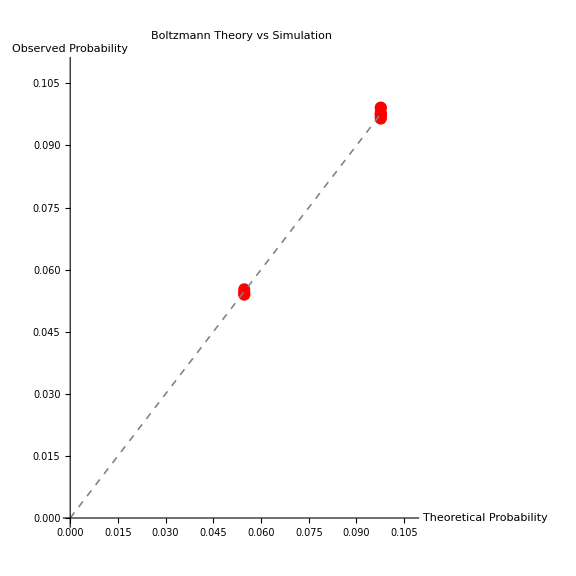

```mathematica
(* =========================================*)(*BOLTZMANN DISTRIBUTION ANALYSIS*)(* =========================================*)(*Step 1:Calculate energy for each state*)

energies=Table[NumericalEnergy[states[[i]]],{i,Length[states]}];

(*Step 2& 3:Calculate Boltzmann distribution*)boltzmannWeights=Exp[-βNum*energies];
partitionFunction=Total[boltzmannWeights];
theoreticalProbs=boltzmannWeights/partitionFunction;

(*Step 4:Get observed probabilities from simulation-FIXED*)observedCounts=Table[If[KeyExistsQ[stateCounts,states[[i]]],stateCounts[states[[i]]],0],{i,Length[states]}];

Print["Observed counts: ",observedCounts];
Print["Total observations: ",Total[observedCounts]];

(*Only calculate probabilities if we have observations*)
If[Total[observedCounts]>0,observedProbs=N[observedCounts/Total[observedCounts]],Print["ERROR: No observations found!"];
observedProbs=Table[0,{Length[states]}];];

(*Scatter plot:theory vs observed*)scatterPlot=ListPlot[Table[{theoreticalProbs[[i]],observedProbs[[i]]},{i,Length[states]}],PlotStyle->{Red,PointSize[0.015]},PlotLabel->"Boltzmann Theory vs Simulation",AxesLabel->{"Theoretical Probability","Observed Probability"},AspectRatio->1,Epilog->{Dashed,Gray,Thickness[0.002],Line[{{0,0},{Max[theoreticalProbs],Max[theoreticalProbs]}}]},ImageSize->Large,PlotRange->{{0,Max[theoreticalProbs]*1.1},{0,Max[observedProbs]*1.1}}];

(*Calculate correlation coefficient*)
correlation=Correlation[theoreticalProbs,observedProbs];

Print["\n"<>StringRepeat["=",60]];
Print["CORRELATION ANALYSIS"];
Print[StringRepeat["=",60]];
Print["Pearson correlation coefficient: ",NumberForm[correlation,{5,4}]];
Print["\n"];
Print[scatterPlot];
```